```mathematica
kC = 3 * 10^10;
kR = 83144626.1815324;            
kHplank = 6.62 * 10^-27;
kb = 1.3807 * 10^-16;
kSt = 6.65210 * 10^-25; 
 kMhydrogen = 1.6735575 * 10^-24;
kStefanBoltzmann = 5.670374419 * 10^-5; 
eV=241799050402417.;
A=(2 kb^4)/(kC^2 kHplank^3);
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
f0[x_]:= Piecewise[{{x^3(1/3-x/8+x^2/62.4),x≤2},{Pi^4/15-Exp[-x](x^3+3 x^2+6x+7.28),x>2}}]
```

0.00762079

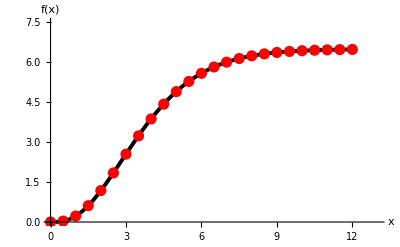

```mathematica
Max[Table[Abs[f[x]-f0[x]],{x,3,5,0.01}]]
F=Table[{x,f0[x]},{x,0,12,0.5}];
Show[Plot[f[x],{x,0,12}, PlotRange->{{0,13},{0,Pi^4/15+1}},PlotStyle->Directive[Black,Thickness[0.007]],AxesStyle->Directive[Black, 17,Arrowheads[.04]],
AxesLabel->{"x","f(x)"}], ListPlot[F, PlotStyle->Directive[Red, PointSize[0.02]]]]
```

```mathematica
T=27.282;
v1=10^17;
v0=0;
A*(f0[ (kHplank v1)/(kb T)]-f0[(kHplank v0)/(kb T)])T^4
kStefanBoltzmann/Pi T^4
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

10.0144

9.99923

```mathematica
R=0.3;
U[r_,kin_,kout_, Q_]:=Q Piecewise[{{1/2 NIntegrate[(1-Exp[-kin(2 √(R^2-r^2(1-μ^2)))])Exp[-kout(r μ-√(R^2-r^2(1-μ^2)))],{μ,√(1-(R/r)^2),1}],r≥R},{NIntegrate[1-Cosh[kin r μ]Exp[-kin √(R^2-r^2(1-μ^2))],{μ,0,1}],r<R}}]
X=Table[i,{i,0,1,0.01}];
{kC/(100*10^-7),kC/(800*10^-7), (kC/(100*10^-7)-kC/(800*10^-7))/20.}//N;
V=Table[v,{v,3.33*10^14,3.*10^15,(kC/(100*10^-7)-kC/(800*10^-7))/50.}];

Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4
absorp[d_,T_,v1_,v0_]:=d/(4 A*Pi*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4)
```

```mathematica
sol=Table[{V[[i]],U[R,absorp[10^-4,1000,V[[i+1]],V[[i]]],absorp[10^-100,1000,V[[i+1]],V[[i]]], Ie[1000,V[[i+1]],V[[i]]]]}, {i,1,Length[V]-1}];
```

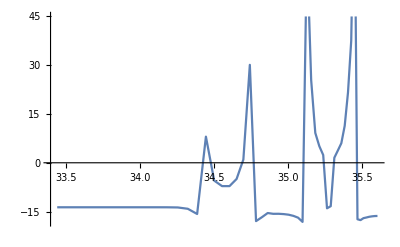

```mathematica
ListLinePlot[Log@sol]
```

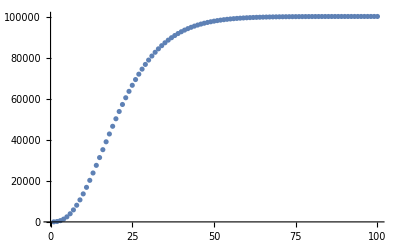

```mathematica
ListPlot[Table[Ie[273,x,0],{x,10^12,10^14,10^12}],PlotRange->All]
```

```mathematica
T=27.282;
v1=3*10^17;
v0=10^17;
Ie[T,v1,v0]
```

General::munfl: Exp[-527234.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
q[x_]:=x^3+3 x^2+6x+7.28
IeLog[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]]
```

```mathematica
IeLog[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175745.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog2[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)+Log[q[V0]]]-Exp[-AA/2(V1-V0)+Log[q[V1]]]]
IeLog2[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-175624.] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
IeLog3[AA_,V0_,V1_]:= Log[A]-AA/2(V0+V1)-AA/4(V1-V0)+Log[Exp[3/2 AA/2(V1-V0)+Log[q[V0]]]-Exp[-1/2 AA/2(V1-V0)+Log[q[V1]]]]
IeLog3[kHplank/(kb T),v0,v1]
```

General::munfl: Exp[-87751.7] is too small to represent as a normalized machine number; precision may be lost.

-175640.

```mathematica
3/2(kHplank/(kb T))/2(v1-v0)+Log[q[v0]]
```

263735.

```mathematica
q0[x_]:=x^3(1/3-x/8+x^2/62.4)
IeLog5[AA_,V0_,V1_]:= 
Piecewise[{{Log[A*(q0[AA*V1]-q0[AA*V0])],AA*V1≤2},{Piecewise[{{ Log[A]-AA/2(V0+V1)+Log[Exp[AA/2(V1-V0)]q[V0]-Exp[-AA/2(V1-V0)]q[V1]],AA/2(V1-V0)<700},{Log[A]-AA/2(V0+V1)+AA/2(V1-V0)+Log[q[V0]],AA/2(V1-V0)>=700}}],AA*V1>2}}]
```

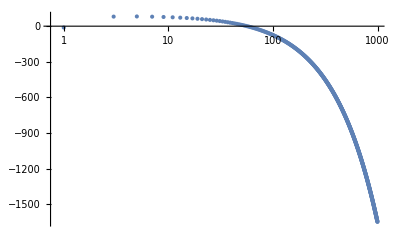

```mathematica
ListLogLinearPlot[Table[{x/10^14,Re@IeLog5[kHplank/(kb T*100),x-2*10^14,x]},{x,10^14,10^17,2*10^14}],PlotRange->All]
```

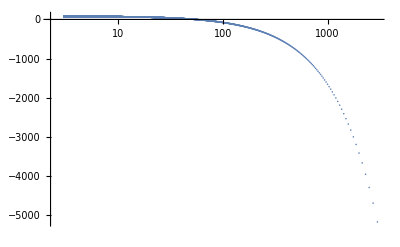

```mathematica
ListLogLinearPlot[Table[{(kC/λ)/10^14,IeLog5[kHplank/(kb T*100),kC/λ,kC/(λ-0.999*10^-7)]},{λ,1000*10^-7,0.1*10^-7,-0.1*10^-7}],PlotRange->All]
```

```mathematica
kStefanBoltzmann*T^4/Pi
Ie[T,10^14,0]
IeLog5[kHplank/(kb T),0,10^14]
```

9.99923

10.0144

-10.8066

```mathematica
(*Ie[T_,v1_,v0_]:=A*(f[ (kHplank v1)/(kb T)]-f[(kHplank v0)/(kb T)])T^4*)
IeExp[AA_,V0_,V1_]:= A(Exp[-AA V0]q[V0]-Exp[-AA(V1)]q[V1])
IeExp[kHplank/(kb T),0,10^14]*T^4
Exp@IeLog5[kHplank/(kb T),0,10^20]*T^4
```

11.2266

11.2266

```mathematica
Table[x/10^14,{x,10^14,10^17,2*10^14}]//N
Table[λ,{λ,1000*10^-7,3*10^-7,-1*10^-7}]//N
```

{1.,3.,5.,7.,9.,11.,13.,15.,17.,19.,21.,23.,25.,27.,29.,31.,33.,35.,37.,39.,41.,43.,45.,47.,49.,51.,53.,55.,57.,59.,61.,63.,65.,67.,69.,71.,73.,75.,77.,79.,81.,83.,85.,87.,89.,91.,93.,95.,97.,99.,101.,103.,105.,107.,109.,111.,113.,115.,117.,119.,121.,123.,125.,127.,129.,131.,133.,135.,137.,139.,141.,143.,145.,147.,149.,151.,153.,155.,157.,159.,161.,163.,165.,167.,169.,171.,173.,175.,177.,179.,181.,183.,185.,187.,189.,191.,193.,195.,197.,199.,201.,203.,205.,207.,209.,211.,213.,215.,217.,219.,221.,223.,225.,227.,229.,231.,233.,235.,237.,239.,241.,243.,245.,247.,249.,251.,253.,255.,257.,259.,261.,263.,265.,267.,269.,271.,273.,275.,277.,279.,281.,283.,285.,287.,289.,291.,293.,295.,297.,299.,301.,303.,305.,307.,309.,311.,313.,315.,317.,319.,321.,323.,325.,327.,329.,331.,333.,335.,337.,339.,341.,343.,345.,347.,349.,351.,353.,355.,357.,359.,361.,363.,365.,367.,369.,371.,373.,375.,377.,379.,381.,383.,385.,387.,389.,391.,393.,395.,397.,399.,401.,403.,405.,407.,409.,411.,413.,415.,417.,419.,421.,423.,425.,427.,429.,431.,433.,435.,437.,439.,441.,443.,445.,447.,449.,451.,453.,455.,457.,459.,461.,463.,465.,467.,469.,471.,473.,475.,477.,479.,481.,483.,485.,487.,489.,491.,493.,495.,497.,499.,501.,503.,505.,507.,509.,511.,513.,515.,517.,519.,521.,523.,525.,527.,529.,531.,533.,535.,537.,539.,541.,543.,545.,547.,549.,551.,553.,555.,557.,559.,561.,563.,565.,567.,569.,571.,573.,575.,577.,579.,581.,583.,585.,587.,589.,591.,593.,595.,597.,599.,601.,603.,605.,607.,609.,611.,613.,615.,617.,619.,621.,623.,625.,627.,629.,631.,633.,635.,637.,639.,641.,643.,645.,647.,649.,651.,653.,655.,657.,659.,661.,663.,665.,667.,669.,671.,673.,675.,677.,679.,681.,683.,685.,687.,689.,691.,693.,695.,697.,699.,701.,703.,705.,707.,709.,711.,713.,715.,717.,719.,721.,723.,725.,727.,729.,731.,733.,735.,737.,739.,741.,743.,745.,747.,749.,751.,753.,755.,757.,759.,761.,763.,765.,767.,769.,771.,773.,775.,777.,779.,781.,783.,785.,787.,789.,791.,793.,795.,797.,799.,801.,803.,805.,807.,809.,811.,813.,815.,817.,819.,821.,823.,825.,827.,829.,831.,833.,835.,837.,839.,841.,843.,845.,847.,849.,851.,853.,855.,857.,859.,861.,863.,865.,867.,869.,871.,873.,875.,877.,879.,881.,883.,885.,887.,889.,891.,893.,895.,897.,899.,901.,903.,905.,907.,909.,911.,913.,915.,917.,919.,921.,923.,925.,927.,929.,931.,933.,935.,937.,939.,941.,943.,945.,947.,949.,951.,953.,955.,957.,959.,961.,963.,965.,967.,969.,971.,973.,975.,977.,979.,981.,983.,985.,987.,989.,991.,993.,995.,997.,999.}

{0.0001,0.0000999,0.0000998,0.0000997,0.0000996,0.0000995,0.0000994,0.0000993,0.0000992,0.0000991,0.000099,0.0000989,0.0000988,0.0000987,0.0000986,0.0000985,0.0000984,0.0000983,0.0000982,0.0000981,0.000098,0.0000979,0.0000978,0.0000977,0.0000976,0.0000975,0.0000974,0.0000973,0.0000972,0.0000971,0.000097,0.0000969,0.0000968,0.0000967,0.0000966,0.0000965,0.0000964,0.0000963,0.0000962,0.0000961,0.000096,0.0000959,0.0000958,0.0000957,0.0000956,0.0000955,0.0000954,0.0000953,0.0000952,0.0000951,0.000095,0.0000949,0.0000948,0.0000947,0.0000946,0.0000945,0.0000944,0.0000943,0.0000942,0.0000941,0.000094,0.0000939,0.0000938,0.0000937,0.0000936,0.0000935,0.0000934,0.0000933,0.0000932,0.0000931,0.000093,0.0000929,0.0000928,0.0000927,0.0000926,0.0000925,0.0000924,0.0000923,0.0000922,0.0000921,0.000092,0.0000919,0.0000918,0.0000917,0.0000916,0.0000915,0.0000914,0.0000913,0.0000912,0.0000911,0.000091,0.0000909,0.0000908,0.0000907,0.0000906,0.0000905,0.0000904,0.0000903,0.0000902,0.0000901,0.00009,0.0000899,0.0000898,0.0000897,0.0000896,0.0000895,0.0000894,0.0000893,0.0000892,0.0000891,0.000089,0.0000889,0.0000888,0.0000887,0.0000886,0.0000885,0.0000884,0.0000883,0.0000882,0.0000881,0.000088,0.0000879,0.0000878,0.0000877,0.0000876,0.0000875,0.0000874,0.0000873,0.0000872,0.0000871,0.000087,0.0000869,0.0000868,0.0000867,0.0000866,0.0000865,0.0000864,0.0000863,0.0000862,0.0000861,0.000086,0.0000859,0.0000858,0.0000857,0.0000856,0.0000855,0.0000854,0.0000853,0.0000852,0.0000851,0.000085,0.0000849,0.0000848,0.0000847,0.0000846,0.0000845,0.0000844,0.0000843,0.0000842,0.0000841,0.000084,0.0000839,0.0000838,0.0000837,0.0000836,0.0000835,0.0000834,0.0000833,0.0000832,0.0000831,0.000083,0.0000829,0.0000828,0.0000827,0.0000826,0.0000825,0.0000824,0.0000823,0.0000822,0.0000821,0.000082,0.0000819,0.0000818,0.0000817,0.0000816,0.0000815,0.0000814,0.0000813,0.0000812,0.0000811,0.000081,0.0000809,0.0000808,0.0000807,0.0000806,0.0000805,0.0000804,0.0000803,0.0000802,0.0000801,0.00008,0.0000799,0.0000798,0.0000797,0.0000796,0.0000795,0.0000794,0.0000793,0.0000792,0.0000791,0.000079,0.0000789,0.0000788,0.0000787,0.0000786,0.0000785,0.0000784,0.0000783,0.0000782,0.0000781,0.000078,0.0000779,0.0000778,0.0000777,0.0000776,0.0000775,0.0000774,0.0000773,0.0000772,0.0000771,0.000077,0.0000769,0.0000768,0.0000767,0.0000766,0.0000765,0.0000764,0.0000763,0.0000762,0.0000761,0.000076,0.0000759,0.0000758,0.0000757,0.0000756,0.0000755,0.0000754,0.0000753,0.0000752,0.0000751,0.000075,0.0000749,0.0000748,0.0000747,0.0000746,0.0000745,0.0000744,0.0000743,0.0000742,0.0000741,0.000074,0.0000739,0.0000738,0.0000737,0.0000736,0.0000735,0.0000734,0.0000733,0.0000732,0.0000731,0.000073,0.0000729,0.0000728,0.0000727,0.0000726,0.0000725,0.0000724,0.0000723,0.0000722,0.0000721,0.000072,0.0000719,0.0000718,0.0000717,0.0000716,0.0000715,0.0000714,0.0000713,0.0000712,0.0000711,0.000071,0.0000709,0.0000708,0.0000707,0.0000706,0.0000705,0.0000704,0.0000703,0.0000702,0.0000701,0.00007,0.0000699,0.0000698,0.0000697,0.0000696,0.0000695,0.0000694,0.0000693,0.0000692,0.0000691,0.000069,0.0000689,0.0000688,0.0000687,0.0000686,0.0000685,0.0000684,0.0000683,0.0000682,0.0000681,0.000068,0.0000679,0.0000678,0.0000677,0.0000676,0.0000675,0.0000674,0.0000673,0.0000672,0.0000671,0.000067,0.0000669,0.0000668,0.0000667,0.0000666,0.0000665,0.0000664,0.0000663,0.0000662,0.0000661,0.000066,0.0000659,0.0000658,0.0000657,0.0000656,0.0000655,0.0000654,0.0000653,0.0000652,0.0000651,0.000065,0.0000649,0.0000648,0.0000647,0.0000646,0.0000645,0.0000644,0.0000643,0.0000642,0.0000641,0.000064,0.0000639,0.0000638,0.0000637,0.0000636,0.0000635,0.0000634,0.0000633,0.0000632,0.0000631,0.000063,0.0000629,0.0000628,0.0000627,0.0000626,0.0000625,0.0000624,0.0000623,0.0000622,0.0000621,0.000062,0.0000619,0.0000618,0.0000617,0.0000616,0.0000615,0.0000614,0.0000613,0.0000612,0.0000611,0.000061,0.0000609,0.0000608,0.0000607,0.0000606,0.0000605,0.0000604,0.0000603,0.0000602,0.0000601,0.00006,0.0000599,0.0000598,0.0000597,0.0000596,0.0000595,0.0000594,0.0000593,0.0000592,0.0000591,0.000059,0.0000589,0.0000588,0.0000587,0.0000586,0.0000585,0.0000584,0.0000583,0.0000582,0.0000581,0.000058,0.0000579,0.0000578,0.0000577,0.0000576,0.0000575,0.0000574,0.0000573,0.0000572,0.0000571,0.000057,0.0000569,0.0000568,0.0000567,0.0000566,0.0000565,0.0000564,0.0000563,0.0000562,0.0000561,0.000056,0.0000559,0.0000558,0.0000557,0.0000556,0.0000555,0.0000554,0.0000553,0.0000552,0.0000551,0.000055,0.0000549,0.0000548,0.0000547,0.0000546,0.0000545,0.0000544,0.0000543,0.0000542,0.0000541,0.000054,0.0000539,0.0000538,0.0000537,0.0000536,0.0000535,0.0000534,0.0000533,0.0000532,0.0000531,0.000053,0.0000529,0.0000528,0.0000527,0.0000526,0.0000525,0.0000524,0.0000523,0.0000522,0.0000521,0.000052,0.0000519,0.0000518,0.0000517,0.0000516,0.0000515,0.0000514,0.0000513,0.0000512,0.0000511,0.000051,0.0000509,0.0000508,0.0000507,0.0000506,0.0000505,0.0000504,0.0000503,0.0000502,0.0000501,0.00005,0.0000499,0.0000498,0.0000497,0.0000496,0.0000495,0.0000494,0.0000493,0.0000492,0.0000491,0.000049,0.0000489,0.0000488,0.0000487,0.0000486,0.0000485,0.0000484,0.0000483,0.0000482,0.0000481,0.000048,0.0000479,0.0000478,0.0000477,0.0000476,0.0000475,0.0000474,0.0000473,0.0000472,0.0000471,0.000047,0.0000469,0.0000468,0.0000467,0.0000466,0.0000465,0.0000464,0.0000463,0.0000462,0.0000461,0.000046,0.0000459,0.0000458,0.0000457,0.0000456,0.0000455,0.0000454,0.0000453,0.0000452,0.0000451,0.000045,0.0000449,0.0000448,0.0000447,0.0000446,0.0000445,0.0000444,0.0000443,0.0000442,0.0000441,0.000044,0.0000439,0.0000438,0.0000437,0.0000436,0.0000435,0.0000434,0.0000433,0.0000432,0.0000431,0.000043,0.0000429,0.0000428,0.0000427,0.0000426,0.0000425,0.0000424,0.0000423,0.0000422,0.0000421,0.000042,0.0000419,0.0000418,0.0000417,0.0000416,0.0000415,0.0000414,0.0000413,0.0000412,0.0000411,0.000041,0.0000409,0.0000408,0.0000407,0.0000406,0.0000405,0.0000404,0.0000403,0.0000402,0.0000401,0.00004,0.0000399,0.0000398,0.0000397,0.0000396,0.0000395,0.0000394,0.0000393,0.0000392,0.0000391,0.000039,0.0000389,0.0000388,0.0000387,0.0000386,0.0000385,0.0000384,0.0000383,0.0000382,0.0000381,0.000038,0.0000379,0.0000378,0.0000377,0.0000376,0.0000375,0.0000374,0.0000373,0.0000372,0.0000371,0.000037,0.0000369,0.0000368,0.0000367,0.0000366,0.0000365,0.0000364,0.0000363,0.0000362,0.0000361,0.000036,0.0000359,0.0000358,0.0000357,0.0000356,0.0000355,0.0000354,0.0000353,0.0000352,0.0000351,0.000035,0.0000349,0.0000348,0.0000347,0.0000346,0.0000345,0.0000344,0.0000343,0.0000342,0.0000341,0.000034,0.0000339,0.0000338,0.0000337,0.0000336,0.0000335,0.0000334,0.0000333,0.0000332,0.0000331,0.000033,0.0000329,0.0000328,0.0000327,0.0000326,0.0000325,0.0000324,0.0000323,0.0000322,0.0000321,0.000032,0.0000319,0.0000318,0.0000317,0.0000316,0.0000315,0.0000314,0.0000313,0.0000312,0.0000311,0.000031,0.0000309,0.0000308,0.0000307,0.0000306,0.0000305,0.0000304,0.0000303,0.0000302,0.0000301,0.00003,0.0000299,0.0000298,0.0000297,0.0000296,0.0000295,0.0000294,0.0000293,0.0000292,0.0000291,0.000029,0.0000289,0.0000288,0.0000287,0.0000286,0.0000285,0.0000284,0.0000283,0.0000282,0.0000281,0.000028,0.0000279,0.0000278,0.0000277,0.0000276,0.0000275,0.0000274,0.0000273,0.0000272,0.0000271,0.000027,0.0000269,0.0000268,0.0000267,0.0000266,0.0000265,0.0000264,0.0000263,0.0000262,0.0000261,0.000026,0.0000259,0.0000258,0.0000257,0.0000256,0.0000255,0.0000254,0.0000253,0.0000252,0.0000251,0.000025,0.0000249,0.0000248,0.0000247,0.0000246,0.0000245,0.0000244,0.0000243,0.0000242,0.0000241,0.000024,0.0000239,0.0000238,0.0000237,0.0000236,0.0000235,0.0000234,0.0000233,0.0000232,0.0000231,0.000023,0.0000229,0.0000228,0.0000227,0.0000226,0.0000225,0.0000224,0.0000223,0.0000222,0.0000221,0.000022,0.0000219,0.0000218,0.0000217,0.0000216,0.0000215,0.0000214,0.0000213,0.0000212,0.0000211,0.000021,0.0000209,0.0000208,0.0000207,0.0000206,0.0000205,0.0000204,0.0000203,0.0000202,0.0000201,0.00002,0.0000199,0.0000198,0.0000197,0.0000196,0.0000195,0.0000194,0.0000193,0.0000192,0.0000191,0.000019,0.0000189,0.0000188,0.0000187,0.0000186,0.0000185,0.0000184,0.0000183,0.0000182,0.0000181,0.000018,0.0000179,0.0000178,0.0000177,0.0000176,0.0000175,0.0000174,0.0000173,0.0000172,0.0000171,0.000017,0.0000169,0.0000168,0.0000167,0.0000166,0.0000165,0.0000164,0.0000163,0.0000162,0.0000161,0.000016,0.0000159,0.0000158,0.0000157,0.0000156,0.0000155,0.0000154,0.0000153,0.0000152,0.0000151,0.000015,0.0000149,0.0000148,0.0000147,0.0000146,0.0000145,0.0000144,0.0000143,0.0000142,0.0000141,0.000014,0.0000139,0.0000138,0.0000137,0.0000136,0.0000135,0.0000134,0.0000133,0.0000132,0.0000131,0.000013,0.0000129,0.0000128,0.0000127,0.0000126,0.0000125,0.0000124,0.0000123,0.0000122,0.0000121,0.000012,0.0000119,0.0000118,0.0000117,0.0000116,0.0000115,0.0000114,0.0000113,0.0000112,0.0000111,0.000011,0.0000109,0.0000108,0.0000107,0.0000106,0.0000105,0.0000104,0.0000103,0.0000102,0.0000101,0.00001,9.9×10^-6,9.8×10^-6,9.7×10^-6,9.6×10^-6,9.5×10^-6,9.4×10^-6,9.3×10^-6,9.2×10^-6,9.1×10^-6,9.×10^-6,8.9×10^-6,8.8×10^-6,8.7×10^-6,8.6×10^-6,8.5×10^-6,8.4×10^-6,8.3×10^-6,8.2×10^-6,8.1×10^-6,8.×10^-6,7.9×10^-6,7.8×10^-6,7.7×10^-6,7.6×10^-6,7.5×10^-6,7.4×10^-6,7.3×10^-6,7.2×10^-6,7.1×10^-6,7.×10^-6,6.9×10^-6,6.8×10^-6,6.7×10^-6,6.6×10^-6,6.5×10^-6,6.4×10^-6,6.3×10^-6,6.2×10^-6,6.1×10^-6,6.×10^-6,5.9×10^-6,5.8×10^-6,5.7×10^-6,5.6×10^-6,5.5×10^-6,5.4×10^-6,5.3×10^-6,5.2×10^-6,5.1×10^-6,5.×10^-6,4.9×10^-6,4.8×10^-6,4.7×10^-6,4.6×10^-6,4.5×10^-6,4.4×10^-6,4.3×10^-6,4.2×10^-6,4.1×10^-6,4.×10^-6,3.9×10^-6,3.8×10^-6,3.7×10^-6,3.6×10^-6,3.5×10^-6,3.4×10^-6,3.3×10^-6,3.2×10^-6,3.1×10^-6,3.×10^-6,2.9×10^-6,2.8×10^-6,2.7×10^-6,2.6×10^-6,2.5×10^-6,2.4×10^-6,2.3×10^-6,2.2×10^-6,2.1×10^-6,2.×10^-6,1.9×10^-6,1.8×10^-6,1.7×10^-6,1.6×10^-6,1.5×10^-6,1.4×10^-6,1.3×10^-6,1.2×10^-6,1.1×10^-6,1.×10^-6,9.×10^-7,8.×10^-7,7.×10^-7,6.×10^-7,5.×10^-7,4.×10^-7,3.×10^-7}